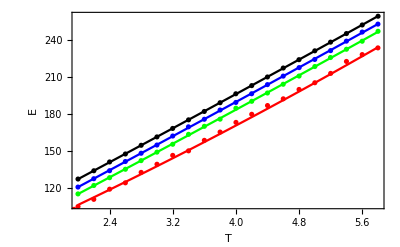

```mathematica
data0={{2.000203,127.332653},{2.200699,134.038268},{2.400131,141.190298},{2.600184,147.661154},{2.800197,154.709858},{2.999878,161.491082},{3.199191,168.374536},{3.400229,175.344447},{3.599688,182.149512},{3.799947,189.251006},{3.999112,196.49581},{4.200496,203.114233},{4.39955,210.117392},{4.599912,217.398214},{4.799108,224.148532},{4.99945,231.334955},
{5.198955,238.396578},{5.400147,245.345694},{5.600399,252.320976},{5.800901,259.408683}};
data025={{1.999619,120.810823},{2.199952,127.585653},{2.40014,134.099588},{2.599698,141.547214},{2.799722,148.254796},{2.999985,154.914008},{3.199923,162.235487},{3.399088,169.677768},{3.600124,175.831803},{3.799898,183.329712},{3.999692,189.475785},{4.199586,196.520215},{4.399614,203.918278},{4.599583,210.830121},{4.801238,217.727461},{4.998955,224.344223},{5.199705,231.514102},{5.399817,239.199237},{5.599856,246.570539},{5.799082,253.017539}};
data05={{1.999781,115.269088},{2.200636,122.108882},{2.400144,128.417284},{2.600498,135.268306},{2.799189,142.265263},{3.00011,149.152082},{3.199834,155.535322},{3.400251,163.585716},{3.600607,170.096917},{3.79996,175.894717},{4.000215,184.783861},{4.200557,190.395602},{4.399727,197.125088},{4.599202,204.221201},{4.800298,210.870428},{5.000336,218.608006},{5.198575,225.9052},{5.400324,232.627362},{5.59964,239.122808},{5.800483,247.180498}};
data1={{0.100105,57.499698},{0.199892,60.195581},{0.300157,62.104981},{0.400039,62.808798},{0.500092,64.303229},{0.600047,64.5144},{0.699893,66.348875},{0.800007,68.265469},{0.899765,69.507216},{0.999543,73.086121},{1.099749,75.904726},{1.199824,76.368228},{1.299876,82.236749},{1.399527,85.40412},{1.500014,88.348485},{1.600106,94.223191},{1.699247,95.104456},{1.799981,99.459985},{1.899724,103.215722},{1.949959,102.747109},{2.000308,105.01739},{2.199966,110.859244},{2.400638,119.098726},{2.600146,124.252854},{2.79985,132.721892},{3.000554,139.32285},{3.199736,146.520162},{3.400255,150.186029},{3.600555,158.717657},{3.799857,165.434874},{4.000942,173.277313},{4.200544,179.8538},{4.400565,186.950114},{4.600053,192.399856},{4.800007,200.00037},{4.999884,205.436422},{5.200396,213.019874},{5.400404,222.725265},{5.599885,228.284833},{5.799131,233.730334},{5.999742,241.354405},{6.201001,249.572256},{6.399941,254.794138},{6.599691,264.521267},{6.800142,269.545976},{7.000609,275.815967}};
fit1=Fit[data1,{1,x,x^2},x];
fit025=Fit[data025,{1,x,x^2},x];
fit05=Fit[data05,{1,x,x^2},x];
fit0=Fit[data0,{1,x,x^2},x];
Show[Plot[{fit1,fit025,fit05,fit0},{x,2,5.8},PlotStyle->{Red,Blue,Green,Black}],ListPlot[{data1,data025,data05,data0},PlotStyle->{Red,Blue,Green,Black}],Frame->True,FrameLabel->{{HoldForm["E"],None},{HoldForm[T],None}}]
```

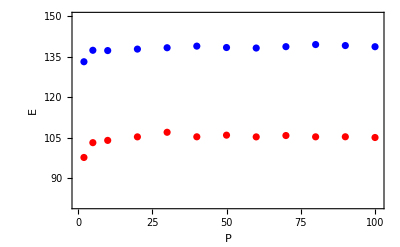

```mathematica
energyPT3={{2,133.09},{5,137.336},{10,137.229},{20,137.78},{30,138.281},{40,138.88},{50,138.36},{60,138.173},{70,138.68},{80,139.46},{90,139.089},{100,138.663}};(*T=3*)
energyPT2={{2,97.6},{5,103.09},{10,103.93},{20,105.24},{30,106.94},{40,105.26},{50,105.87},{60,105.23},{70,105.73},{80,105.25},{90,105.27},{100,105}};(*T=2*)
ListPlot[{energyPT3,energyPT2},PlotRange->{{0,101},{80,150}},PlotStyle->{Blue,Red},Frame->True,FrameLabel->{{HoldForm["E"],None},{HoldForm[P],None}},LabelStyle->{15,GrayLevel[0]}]
```